# ***** NAZARIO METHOD FOR EVALUATION OF SPECTRAL DENSITY *****

## Inputs

### Input parameters

```mathematica
Estar = 0.5;
S = 0.1;
tmax = 9;
```

### Target function

```mathematica
DeltaS[En_] = Exp[-(En-Estar)^2/(2*S^2)]/(Sqrt[2*Pi]*S*1/2*(1+Erf[Estar/(Sqrt[2]*S)]))
```

3.98942 ⅇ^(-50. (-0.5+En)^2)

```mathematica
Clear[BinsOm]
BinsOm=Table[Range[-1,2,0.01]];
```

```mathematica
sdata1 = Transpose@{BinsOm, DeltaS[BinsOm]};
```

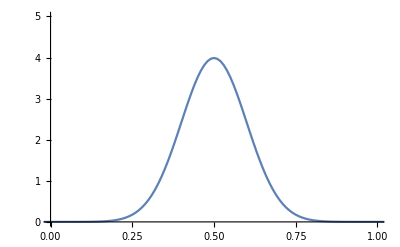

```mathematica
ListLinePlot[sdata1, PlotRange->{{0,1},{0,5}}]
```

### Basis function and creation of the bins of t

```mathematica
Clear[b]
b[En_, t_] = E^(-t*En)
```

ⅇ^(-En t)

```mathematica
Clear[Binst]
Binst = Table[Range[0, tmax, 1]];
```

```mathematica
Clear[NBins]
NBinsA = Dimensions[Binst];
NBins = NBinsA[[1]];
```

## Computation of the integrals for the evaluation of R, f, W^-1

```mathematica
For[j=1, j<=NBins, j++, RVec[j] = Table[Integrate[b[K, j],{K, 0, Infinity}]]]
```

```mathematica
Clear[WMatrix]
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, WMatrix[i,j] = Table[Integrate[b[K,i]*b[K,j],{K, 0, Infinity}]]]]
Clear[WM]
WM = Table[WMatrix[i,j],{i,1,NBins},{j,1,NBins}];
Clear[WMM1]
WMM1 = Inverse[WM];
```

```mathematica
Dimensions[WMM1];
```

```mathematica
For[j=1, j<=NBins, j++,fVec[j]=0];
For[j=1, j<=NBins, j++, fVec[j] = Table[Limit[Integrate[b[K, j]*DeltaS[K],K], K-> Infinity]-  Limit[Integrate[b[K, j]*DeltaS[K],K], K-> 0]]]
```

## Evaluation of the coefficients g_t and plot as a function of t

### Computation of g_t for each Bin of t as the combination of three terms

```mathematica
For[j=1, j<=NBins, j++,g1[j]=0];
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, g1[j] = g1[j] +fVec[i]*WMM1[[j,i]]]; Print[N[g1[j],10]]]
```

-7.82271

464.915

-8711.84

75482.8

-353476.

962458.

-1.56377×10^6

1.49177×10^6

-770337.

166134.

```mathematica
For[j=1, j<=NBins, j++,g1[j]=0];
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, g1[j] = g1[j] +fVec[i]*WMM1[[j,i]]]]
```

```mathematica
For[j=1, j<=NBins, j++,g2A[j]=0]
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, g2A[j] = g2A[j] +RVec[i]*WMM1[[j,i]]]]
```

```mathematica
g2NScal=0;
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, g2NScal = g2NScal+(RVec[j]*fVec[i])*WMM1[[j,i]]]]
```

```mathematica
N[g2NScal,10];
```

```mathematica
g2DScal = 0;
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, g2DScal = g2DScal+(RVec[j]*RVec[i])*WMM1[[j,i]]]]
N[g2DScal]
```

5.85794

```mathematica
Clear[qFin]
For[j=1, j<=NBins, j++, qFin[j] = g1[j] + g2A[j]*g2NScal/g2DScal]
```

### Plot of g_t for each bin of t

```mathematica
Clear[qPlot]
qPlot = Table[qFin[j], {j,1,NBins}]
```

{9.76165,-9.86303,-3225.53,41879.1,-232503.,693628.,-1.1907×10^6,1.17699×10^6,-622664.,136599.}

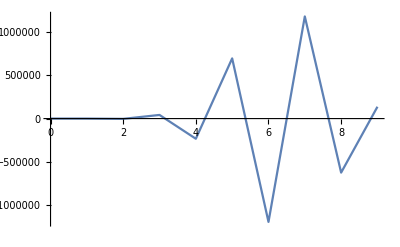

```mathematica
ListLinePlot[Transpose@{Binst, qPlot}]
```

## Computation of DeltaBar and comparison with the target function

```mathematica
DeltaBar[Om_] = Sum[qFin[i]*b[Om,i],{i,NBins}]
```

136599. ⅇ^(-10 Om)-622664. ⅇ^(-9 Om)+1.17699×10^6 ⅇ^(-8 Om)-1.1907×10^6 ⅇ^(-7 Om)+693628. ⅇ^(-6 Om)-232503. ⅇ^(-5 Om)+41879.1 ⅇ^(-4 Om)-3225.53 ⅇ^(-3 Om)-9.86303 ⅇ^(-2 Om)+9.76165 ⅇ^-Om

```mathematica
N[DeltaBar[1],10]
```

-0.137988

```mathematica
Diff [Om_] = DeltaS[Om]-DeltaBar[Om]
```

3.98942 ⅇ^(-50. (-0.5+Om)^2)-136599. ⅇ^(-10 Om)+622664. ⅇ^(-9 Om)-1.17699×10^6 ⅇ^(-8 Om)+1.1907×10^6 ⅇ^(-7 Om)-693628. ⅇ^(-6 Om)+232503. ⅇ^(-5 Om)-41879.1 ⅇ^(-4 Om)+3225.53 ⅇ^(-3 Om)+9.86303 ⅇ^(-2 Om)-9.76165 ⅇ^-Om

```mathematica
Binnaggio = Range[-2, 20, 0.01];
```

```mathematica
BBB = Table[Binnaggio];
```

```mathematica
AAA =Table[DeltaBar[Binnaggio]];
```

```mathematica
sdata = Transpose@{BBB, AAA};
```

```mathematica
sdatadiff = Transpose@{BBB, Table[Diff[Binnaggio]]};
```

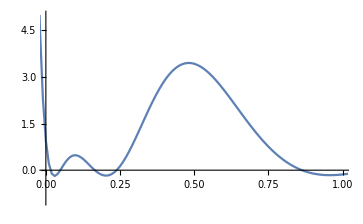

```mathematica
ListLinePlot[sdata,PlotRange->{{0,1},{-1,5}}]
```

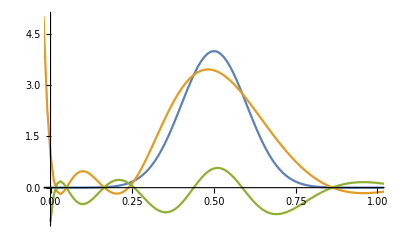

```mathematica
ListLinePlot[{sdata1,sdata, sdatadiff},PlotRange->{{0,1},{-1,5}}]
```